```mathematica
ClearAll["Global`*"]
pars={m->1,l->1,g->9.81};
Needs["VariationalMethods`"];
T[t_]=1/2 m l^2 θ'[t]^2;
V[t_]=-m g l Cos[θ[t]];
L[t_]=T[t]-V[t];
eqn=EulerEquations[L[t], θ[t], t]/.{0->F[t]}
pend= NonlinearStateSpaceModel[eqn/.pars,{θ[t]},{F[t]},{θ[t],θ'[t]},t]
```

-l m (g Sin[θ[t]]+l θ''[t])==F[t]

x_2[t]-F[t]-9.81 Sin[x_1[t]]x_1[t]x_2[t]x_1[t]x_2[t] 2122NoneNoneFalseFalseFalse{F[t]}t

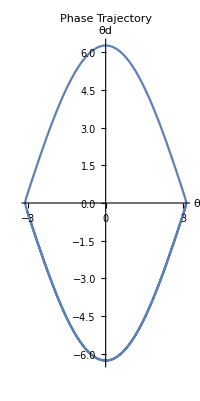

```mathematica
resp=OutputResponse[{pend/.pars,{0.99Pi,0}},0,{t,0,10}];
ParametricPlot[resp,{t,0,10},PlotLabel->"Phase Trajectory",AxesLabel->{"θ","θd"}]
```

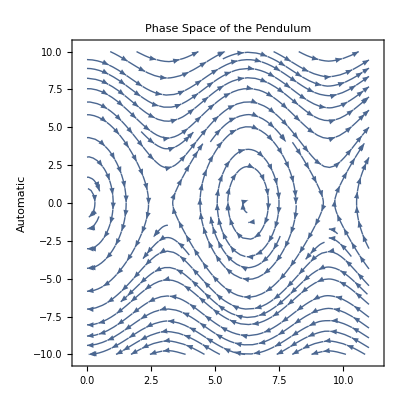

```mathematica
StreamPlot[{y,-9.8 Sin[x]},{x,0,3.5*Pi},{y,-10,10},PlotLabel->"Phase Space of the Pendulum",AxesLabel->Automatic]
```